# Числено интегриране. Квадратурни формули на Нютон-Коутс

Задача: (a и b са съответно предпоследната и последната цифра от факултетния номер)
Дадена е функцията f(x) = (b + 2 - x)/(2 x^2+a+1)
1. Табулирайте функцията f(x) в интервала [a, a+b+1], като разделите интервала на b+5 равни части.
2. Пресметнете ∫_a^(a+b+1) f(x)ⅆx по формулата на левите правоъгълници, използвайки точките получени в 1. Каква е грешката на полученото приближение?
3. Пресметнете ∫_a^(a+b+1) f(x)ⅆx по формулата на десните правоъгълници, използвайки точките получени в 1. Каква е грешката на полученото приближение?
4. Пресметнете ∫_a^(a+b+1) f(x)ⅆx по формулата на средните правоъгълници, използвайки точките получени в 1. Каква е грешката на полученото приближение?
5. Пресметнете ∫_a^(a+b+1) f(x)ⅆx по формулата на трапеците, използвайки точките получени в 1. Каква е грешката на полученото приближение?
6. Може ли по построената в 1 таблица да се използва квадратурната формула на Симпсън за изчисляване на интеграла ∫_a^(a+b+1) f(x)ⅆx? Обосновете отговора си. Ако може, го изчислете и пресметнете каква е грешката на полученото приближение?
7. Пресметнете ∫_a^(a+b+1) f(x)ⅆx по формулата на левите правоъгълници с точност 0.00001.
8. Пресметнете ∫_a^(a+b+1) f(x)ⅆx по формулата на десните правоъгълници с точност 0.00001.
9. Пресметнете ∫_a^(a+b+1) f(x)ⅆx по формулата на средните правоъгълници с точност 0.00001.
10. Пресметнете ∫_a^(a+b+1) f(x)ⅆx по формулата на трапеците с точност 0.00001.
11. Пресметнете ∫_a^(a+b+1) f(x)ⅆx по формулата на Симпсън с точност 0.00001.

## Съставяне на мрежата

```mathematica
f[x_]:=(10-x)/(2 x^2 +1)
a = 0.; b = 10.;
h = (b-a)/n;
n = 14;
Print["Мрежата е с брой подинтервали n = ", n, " и стъпка h = ",h]
xt = Table[a + i*h, {i,0,n}]
```

Мрежата е с брой подинтервали n = 14 и стъпка h = 0.714286

{0.,0.714286,1.42857,2.14286,2.85714,3.57143,4.28571,5.,5.71429,6.42857,7.14286,7.85714,8.57143,9.28571,10.}

```mathematica
f[xt]
```

{10.,4.59596,1.68675,0.771543,0.41225,0.242494,0.151433,0.0980392,0.0646353,0.0426933,0.0277283,0.0172159,0.0096565,0.00411813,8.8376×10^-18}

## Леви правоъгълници

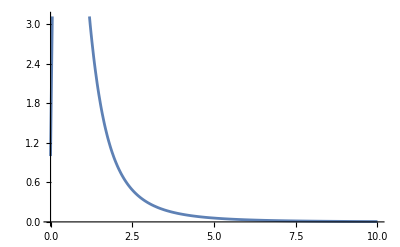

```mathematica
Plot[Abs[f'[x]],{x,a,b}]
```

```mathematica
a = 0.;b= 10.;
h = (b -a)/n;
n = 14;
f[x_]:= (10-x)/(2 x^2 +1)
Itochno = ∫_a^b f[x]ⅆx ;
I1 = h*∑_(i=0)^(n-1) f[a+i*h];
M1 = Abs[f'[a]];
R1 = (b-a)^2/(2n)*M1;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n]
Print["Приближената стойност по формулата на левите правоъгълници е ", I1]
Print["Точната стойност                                           е ", Itochno]
Print["Теоретичната грешка по формулата на левите правоъгълници   е ", R1]
Print["Истинската грешка по формулата на левите правоъгълници     е ", Abs[I1-Itochno]]
```

Мрежата е със стъпка 0.714286 и брой подинтервали 14

Приближената стойност по формулата на левите правоъгълници е 12.9461

Точната стойност                                           е 9.28221

Теоретичната грешка по формулата на левите правоъгълници   е 3.57143

Истинската грешка по формулата на левите правоъгълници     е 3.66387

## Десни правоъгълници

```mathematica
Plot[Abs[f'[x]],{x,a,b}]
```

-Graphics-

```mathematica
a = 0.;b= 10.;
h = (b -a)/n;
n = 14;
f[x_]:= (10-x)/(2 x^2 +1)
Itochno = ∫_a^b f[x]ⅆx ;
I2 = h*∑_(i=0)^n f[a+i*h];
M2 = Abs[f'[a]];
R2 = (b-a)^2/(2n)*M2;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n]
Print["Приближената стойност по формулата на левите правоъгълници е ", I2]
Print["Точната стойност                                           е ", Itochno]
Print["Теоретичната грешка по формулата на левите правоъгълници   е ", R2]
Print["Истинската грешка по формулата на левите правоъгълници     е ", Abs[I2-Itochno]]
```

Мрежата е със стъпка 0.0588568 и брой подинтервали 14

Приближената стойност по формулата на левите правоъгълници е 6.28534

Точната стойност                                           е 9.28221

Теоретичната грешка по формулата на левите правоъгълници   е 3.57143

Истинската грешка по формулата на левите правоъгълници     е 2.99688

## Средни правоъгълници

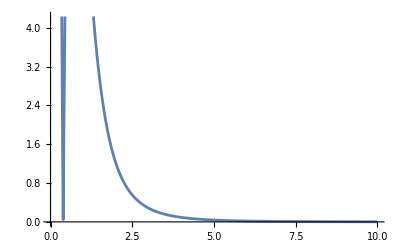

```mathematica
Plot[Abs[f''[x]],{x,a,b}]
```

```mathematica
a = 0.;b= 10.;
h = (b -a)/n;
n = 14;
f[x_]:= (10-x)/(2 x^2 +1)
Itochno = ∫_a^b f[x]ⅆx ;
I3 = h*∑_(i=0)^(n-1) f[a+i*h + h/2];
M3 = Abs[f''[a]];
R3= (b-a)^3/(24 n^2)*M3;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n]
Print["Приближената стойност по формулата на левите правоъгълници е ", I3]
Print["Точната стойност                                           е ", Itochno]
Print["Теоретичната грешка по формулата на левите правоъгълници   е ", R3]
Print["Истинската грешка по формулата на левите правоъгълници     е ", Abs[I3-Itochno]]
```

Мрежата е със стъпка 0.714286 и брой подинтервали 14

Приближената стойност по формулата на левите правоъгълници е 9.21174

Точната стойност                                           е 9.28221

Теоретичната грешка по формулата на левите правоъгълници   е 8.5034

Истинската грешка по формулата на левите правоъгълници     е 0.0704732

## Трапеци

```mathematica
Plot[Abs[f''[x]],{x,a,b}]
```

-Graphics-

```mathematica
a = 0.;b= 10.;
h = (b -a)/n;
n = 14;
f[x_]:= (10-x)/(2 x^2 +1)
Itochno = ∫_a^b f[x]ⅆx ;
IT = h/2*(f[a]+2∑_(i=1)^(n-1) f[a+i*h]+f[b]);
M2 = Abs[f''[a]];
RT = (b-a)^3/(12 n^2)*M2;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n]
Print["Приближената стойност по формулата на трапците е ", IT]
Print["Точната стойност                               е ", Itochno]
Print["Теоретичната грешка по формулата на трапците   е ", RT]
Print["Истинската грешка по формулата на трапците     е ", Abs[IT-Itochno]]
```

Мрежата е със стъпка 0.714286 и брой подинтервали 14

Приближената стойност по формулата на трапците е 9.37465

Точната стойност                               е 9.28221

Теоретичната грешка по формулата на трапците   е 17.0068

Истинската грешка по формулата на трапците     е 0.0924405

## Симпсън

Може да използваме формулата на Симпсън, тъй като броят на подинтервалите е четно число - в случая 14.

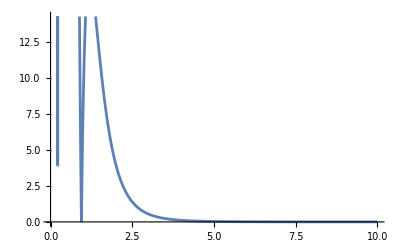

```mathematica
Plot[Abs[f''''[x]],{x,a,b}]
```

```mathematica
a = 0.;b= 10.;
h = (b -a)/n;
n = 14;
f[x_]:= (10-x)/(2 x^2 +1)
Itochno = ∫_a^b f[x]ⅆx ;
m = n /2;
IS = h/3*(f[a]+4∑_(i=1)^m f[a+(2i-1)*h]+2∑_(i=1)^(m-1) f[a+(2i)*h]+f[b]);
M4 = Abs[f''''[a]];
RS = (b-a)^5/(180 n^4)*M4;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n]
Print["Приближената стойност по формулата на Симпсън  е ", IS]
Print["Точната стойност                               е ", Itochno]
Print["Теоретичната грешка по формулата на Симпсън    е ", RS]
Print["Истинската грешка по формулата на Симпсън      е ", Abs[IS-Itochno]]
```

Мрежата е със стъпка 0.714286 и брой подинтервали 14

Приближената стойност по формулата на Симпсън  е 8.99837

Точната стойност                               е 9.28221

Теоретичната грешка по формулата на Симпсън    е 13.8831

Истинската грешка по формулата на Симпсън      е 0.283842

# Пресмятане с предварително зададена точност

## Леви правоъгълници

```mathematica
eps = 10^-5;
Clear[n]
Reduce[(b-a)^2/(2n)*M1<=eps, n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n<0||n≥1.375×10^7

```mathematica
a = 0.;b= 10.;
h = (b -a)/n;
n = 1.375*10^7;
f[x_]:= (10-x)/(2 x^2 +1)
Itochno = ∫_a^b f[x]ⅆx ;
I1 = h*∑_(i=0)^(n-1) f[a+i*h];
M1 = Abs[f'[a]];
R1 = (b-a)^2/(2n)*M1;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n] 
Print["Приближената стойност по формулата на левите правоъгълници е ", I1]
Print["Точната стойност                                           е ", Itochno]
Print["Теоретичната грешка по формулата на левите правоъгълници   е ", R1]
Print["Истинската грешка по формулата на левите правоъгълници     е ", Abs[I1-Itochno]]
```

Мрежата е със стъпка 7.27273×10^-7 и брой подинтервали 1.375×10^7

Приближената стойност по формулата на левите правоъгълници е 9.28222

Точната стойност                                           е 9.28221

Теоретичната грешка по формулата на левите правоъгълници   е 3.63636×10^-6

Истинската грешка по формулата на левите правоъгълници     е 3.63636×10^-6

## Десни правоъгълници

```mathematica
eps = 10^-5;
Clear[n]
Reduce[(b-a)^2/(2n)*M2<=eps, n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n<0||n≥2.×10^8

```mathematica
a = 0.;b= 10.;
h = (b -a)/n;
n= 1.5*10^7;
f[x_]:= (10-x)/(2 x^2 +1)
Itochno = ∫_a^b f[x]ⅆx ;
I2 = h*∑_(i=0)^n f[a+i*h];
M2 = Abs[f'[a]];
R2 = (b-a)^2/(2n)*M2;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n] // N
Print["Приближената стойност по формулата на левите правоъгълници е ", I2]
Print["Точната стойност                                           е ", Itochno]
Print["Теоретичната грешка по формулата на левите правоъгълници   е ", R2]
Print["Истинската грешка по формулата на левите правоъгълници     е ", Abs[I2-Itochno]]
```

Мрежата е със стъпка 6.66667×10^-7 и брой подинтервали 1.5×10^7

Приближената стойност по формулата на левите правоъгълници е 9.28222

Точната стойност                                           е 9.28221

Теоретичната грешка по формулата на левите правоъгълници   е 3.33333×10^-6

Истинската грешка по формулата на левите правоъгълници     е 3.33333×10^-6

## Средни правоъгълници

```mathematica
eps = 10^-5;
Clear[n]
Reduce[(b-a)^3/(24 n^2)*M3<=eps, n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n≤-12909.9||n≥12909.9

```mathematica
a = 0.;b= 10.;

n = 3535.53;
h = (b -a)/n;
f[x_]:=(10-x)/(2 x^2 +1)
Itochno = ∫_a^b f[x]ⅆx ;
I3 = h*∑_(i=0)^(n-1) f[a+i*h + h/2];
M3 = Abs[f''[a]];
R3= (b-a)^3/(24 n^2)*M3;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n]
Print["Приближената стойност по формулата на левите правоъгълници е ", I3]
Print["Точната стойност                                           е ", Itochno]
Print["Теоретичната грешка по формулата на левите правоъгълници   е ", R3]
Print["Истинската грешка по формулата на левите правоъгълници     е ", Abs[I3-Itochno]]
```

Мрежата е със стъпка 0.00282843 и брой подинтервали 3535.53

Приближената стойност по формулата на левите правоъгълници е 9.28221

Точната стойност                                           е 9.28221

Теоретичната грешка по формулата на левите правоъгълници   е 0.000133334

Истинската грешка по формулата на левите правоъгълници     е 3.37267×10^-7

## Трапеци

```mathematica
eps = 10^-5;
Clear[n]
Reduce[(b-a)^3/(12 n^2)*M3<=eps, n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n≤-18257.4||n≥18257.4

```mathematica
a = 0.;b= 10.;

n = 5000;
h = (b -a)/n;
f[x_]:= (10-x)/(2 x^2 +1)
Itochno = ∫_a^b f[x]ⅆx ;
IT = h/2*(f[a]+2∑_(i=1)^(n-1) f[a+i*h]+f[b]);
M2= Abs[f''[a]];
RT = (b-a)^3/(12 n^2)*M2;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n]
Print["Приближената стойност по формулата на трапците е ", IT]
Print["Точната стойност                               е ", Itochno]
Print["Теоретичната грешка по формулата на трапците   е ", RT]
Print["Истинската грешка по формулата на трапците     е ", Abs[IT-Itochno]]
```

Мрежата е със стъпка 0.002 и брой подинтервали 5000

Приближената стойност по формулата на трапците е 9.28221

Точната стойност                               е 9.28221

Теоретичната грешка по формулата на трапците   е 0.000133333

Истинската грешка по формулата на трапците     е 3.31675×10^-7

## Симпсън

```mathematica
eps = 10^-5;
Clear[n]
Reduce[(b-a)^5/(180 n^4)*M4<=eps, n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n≤-480.562||n≥480.562

```mathematica
a = 0.;b= 10.;
n = 169.904;
h = (b -a)/n;
f[x_]:= (10-x)/(2 x^2 +1)
Itochno = ∫_a^b f[x]ⅆx ;
m = n /2;
IS = h/3*(f[a]+4∑_(i=1)^m f[a+(2i-1)*h]+2∑_(i=1)^(m-1) f[a+(2i)*h]+f[b]);
M4 = Abs[f''''[a]];
RS = (b-a)^5/(180 n^4)*M4;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n]
Print["Приближената стойност по формулата на Симпсън  е ", IS]
Print["Точната стойност                               е ", Itochno]
Print["Теоретичната грешка по формулата на Симпсън    е ", RS]
Print["Истинската грешка по формулата на Симпсън      е ", Abs[IS-Itochno]]
```

Мрежата е със стъпка 0.0588568 и брой подинтервали 169.904

Приближената стойност по формулата на Симпсън  е 9.28217

Точната стойност                               е 9.28221

Теоретичната грешка по формулата на Симпсън    е 0.000640006

Истинската грешка по формулата на Симпсън      е 0.0000437095